# Play around: Popup windows and interacting with global scope

## Tests

### Dialog

```mathematica
Dialog[]
```

101

```mathematica
dialogvar=1
```

1

```mathematica
dialogvar+=100
```

101

```mathematica
Return[]
```

### MessageDialog, ChoiceDialog

```mathematica
MessageDialog[{x^3,Graphics[Disk[],ImageSize->Tiny]}];
```

```mathematica
testvar=ChoiceDialog["Pick one",{1->"a",2->"b",3->"c",4->"d"}]
```

### DialogInput (wait until DialogReturn)

```mathematica
res=DialogInput[DialogNotebook[{
TextCell["Click to proceed"],
Button["Proceed 1",DialogReturn[1]],
Button["Proceed 777",DialogReturn[777]]}]]
```

777

```mathematica
res
```

777

### CreateDialog/CreateWindow

```mathematica
CreateDialog[{
TextCell["Enter a name: "],
InputField[Dynamic[nm],String],
DefaultButton[DialogReturn[ret=nm]]
}];
```

```mathematica
ret
```

1258

```mathematica
CreateWindow[DialogNotebook[{
TextCell["Enter a name: "],
InputField[Dynamic[nm],String],
DefaultButton[DialogReturn[ret=nm]]}
]];
```

```mathematica
ret
```

1258

## Functions

```mathematica
testGlobalVariable=787;
```

```mathematica
testGlobalNotebook=SelectedNotebook[]
```

6sn3a_shm29FrontEndObject[LinkObject["6sn3a_shm", 3, 1]]29Play_Popup window.nbC:\prog\_w\NounouW\NounouW\Tests\graphics\Play_Popup window.nb

```mathematica
testFunction[]:=
Module[{(*tempgr*)},
testGlobalNotebook=SelectedNotebook[];
CreateDialog[{
TextCell["Enter a factor: "],
InputField[Dynamic[nm], Number],
ExpressionCell[ Dynamic[tempgr=Plot[Sin[nm*x], {x,0, 4 Pi}, ImageSize-> 72*8]]],
Grid[{{
Button["Print variables",
(*CellPrint[ExpressionCell[{nm}]]    : This does not output, probably tries to print in dialog*)
NotebookWrite[testGlobalNotebook, Cell[ExpressionCell[{nm}],"Output"]];
NotebookWrite[testGlobalNotebook,Cell[ BoxData[ToBoxes[tempgr]], "Output", CellTags-> {"testCT"}]]
],
Button["Print global variable to messages",Print[testGlobalVariable]],
Button["Delete test cell tag",NotebookDelete[NotebookFind[testGlobalNotebook,"testCT",Previous, CellTags][[1]]]
],
DefaultButton[DialogReturn["Hello"]]
}}]
}]
]
```

## Testing Functions

3

10

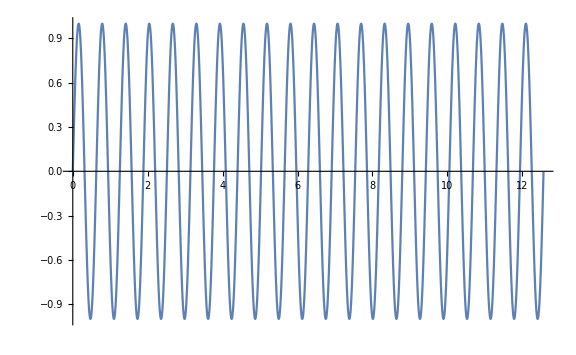

```mathematica
testFunction[];
```

```mathematica
NotebookFind[SelectedNotebook[],"testCT",Previous, CellTags]
```

NotebookSelection[2aaii_shm15FrontEndObject[LinkObject["2aaii_shm", 3, 1]]15Play_Popup window.nbC:\prog\_w\NounouW\NounouW\Tests\graphics\Play_Popup window.nb]

```mathematica
NotebookDelete[NotebookFind[SelectedNotebook[],"testCT",Previous, CellTags][[1]]]
```

```mathematica
NotebookDelete[{}]
```